```mathematica
Block[{currentTotal},	
	TopEditorsFifty[article_] :=
		If[Length@editStats[article] == 2,
			currentTotal := 0;
			For[i = 1, i ≤ Length@editStats[article][[1]], i++,
				If[N@currentTotal / Total[editStats[article][[1]]] ≤ 0.5,
					currentTotal += editStats[article][[1]][[i]],
					Return[i-1];
					Break[]
				]
			],
			currentTotal := 0;
			For[i = 1, i ≤ Length@editStats[article][[1]], i++,
				If[N@currentTotal / 
					(Total[editStats[article][[1]]] + editStats[article][[3]][[2]]) ≤ 0.5,
					currentTotal += editStats[article][[1]][[i]],
					Return[i-1];
					Break[]
				];
				If[i == Length@editStats[article][[1]],
					Return[30]
				]
			]
		]
]
```

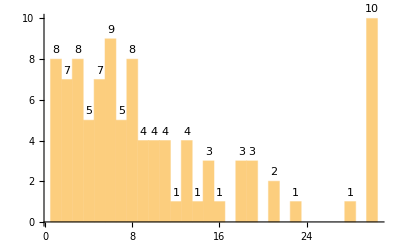

```mathematica
Histogram[AssociationMap[TopEditorsFifty, urlForm], 30, LabelingFunction -> Above]
```